## Alpha 织体

### 多声部平稳进行求最优解

mma 接收的数值为十二平均律值，0  为中央 C（C4），例：

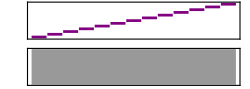

```mathematica
Sound[Table[SoundNote[i],{i,0,12}]]
```

构建 C 大调白键和弦表，按｛根音，三音，五音，七音，九音｝排序

```mathematica
Major={0,4,7,11,14}; (* 大九和弦 *)
Minor={0,3,7,10,14}; (* 小九和弦 *)
Clist={
(* C *) Major,
(* Dm *) Minor+2,
(* Em *) Minor+4,
(* F *) Major+5,
(* G *) Major+7,
(* Am *) Minor+9,
(* Bdim *) {0,3,6,10,13}+11
};
(* 扩充一遍升八度的 *)
Clist=Join[Clist,Clist+12];
```

按分解和弦的规则重排各列顺序｛根音，五音，七音，^根音，九音，^三音，^五音，^七音，^^根音…｝

```mathematica
Colist=Table[{Clist⟦i,1⟧,Clist⟦i,3⟧,Clist⟦i,4⟧,Clist⟦i,1⟧+12,Clist⟦i,5⟧,Clist⟦i,2⟧+12},{i,1,7*2}];
(* 扩充两遍升八度的 *)
Colist=ArrayFlatten[{{Colist,Colist⟦All,2;;6⟧+12,Colist⟦All,2;;6⟧+24}}];
```

错误范例：六部同向的分解和弦

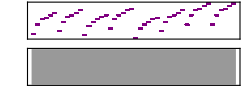

```mathematica
Sound[Table[SoundNote[Colist⟦i,j⟧,.2],
{i,{4,5,3,6,2,5,1+7,1+7}},(* 华语第二用烂的和弦进行 *)
{j,1,6}]]
```

搜索四声部解决方向不全同、最平稳进行的方案
暂时不考虑变底音的情况（最下层总是根音和五音）
设 d 记录了各声部解决方向和距离，+为升高-为降低，scor 对其打分，有保持不变的声部 +1 分，其它无论升降 - 距离/3 分，非零声部中有一升一降对 +0.5 分

```mathematica
scor[d_]:=Count[d,0]-Total[Abs[d]]/3+Min[Count[Positive@d,True],Count[Negative@d,True]]/2
```

输入：pre：前一个和弦已选好的右手 list（自动识别声部个数 n≥1）
fol：后一个和弦的右手的备选 list（m>n）
（两个 list 按从低到高排好序）
（算法暂时就 C_m^n 全试一遍好了反正元素个数又不多…）

```mathematica
Solv[pre_,fol_]:=Module[{
(* 列出所有子集 *)
s=Subsets[fol,{Length[pre]}]},
(* 计算各声部解决方向和距离并取分数最高者 *)
Return[s⟦Ordering[Table[scor[s⟦i⟧-pre],{i,1,Length[s]}],-1]⟧];
]
```

用法举例：从 F 到 G 和弦，F 的右手取 3~5 列，求 G 和弦的平稳进行音

```mathematica
Colist⟦4,3;;5⟧
```

{16,17,19}

```mathematica
Solv[Colist⟦4,3;;5⟧,Colist⟦5⟧]⟦1⟧
```

{14,18,19}

用函数迭代决策出整个和弦进行的右手音
cp：输入简谱的和弦进行（其实是和弦表的行号）
first：输入第一个和弦的右手选择哪几列（≥3，因为最下面俩总是根音和五音）

```mathematica
ChordPro[cp_,first_]:=Module[
{ini=Table[Colist⟦i,3;;16⟧,{i,cp}]}, (* 此处 j 从 3 开始排除了最下面俩音（左手弹的） *)
ini⟦1⟧=ini⟦1,first⟧;
Table[ini⟦n+1⟧=Solv[ini⟦n⟧,ini⟦n+1⟧]⟦1⟧,
{n,1,Length[cp]-1}];
Return[ArrayFlatten[{{Table[Colist⟦i,1;;2⟧,{i,cp}],ini}}] ] (* 此处补回左手音） *)
]
```

使用范例

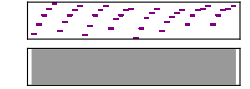

```mathematica
cl=ChordPro[{4,5,3,6,2,5,1+7,1+7} (* 华语第二用烂的和弦进行 *)
,{3,5,6,7}];
Sound[Table[SoundNote[cl⟦i,j⟧,.2],{i,1,8},{j,1,5}]]
```

### 节奏型库